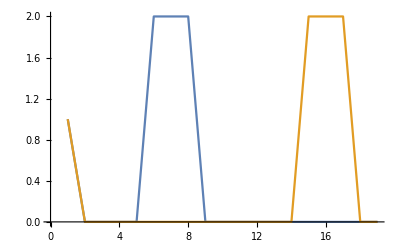

```mathematica
data1=Table[Sin[i/10],{i,0,100}]//N;
data2=Table[Sin[i/10],{i,0-10,100-10}]//N;
data1={1,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0};
data2={1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0};
ListLinePlot[{data1,data2}]
```

```mathematica
G[τ_]:=
Sum[
If[t+τ≤ Length[data1],data1[[t]]*data2[[t+τ]],0]
,{t,1,Length[data1]}]
```

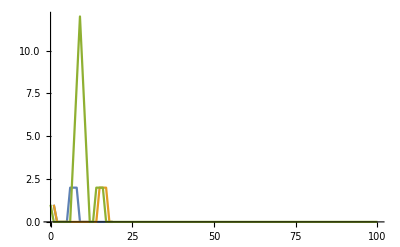

```mathematica
ListLinePlot[
{data1,data2,
Table[{i,G[i]/G[0]//N},{i,0,100}]
},PlotRange->All
]
```

```mathematica
taus=Table[{i,G[i]//N},{i,0,100}];
MaximalBy[taus,#[[2]]&]
```

(9 | 12.)

```mathematica
taus;
```

```mathematica
tests={
{{0.0,1.0},{1.0,0.53772849849},{2.0,0.408257275643},{3.0,0.620192789133},{6.0,0.784608579025},{7.0,0.90760540022},{8.0,0.525385138894},{9.0,0.381559155178},{10.0,0.586787112188},{14.0,0.844272388702},{15.0,0.492078520452},{16.0,0.354276972537},{17.0,0.549162038983},{20.0,0.680915805957},{21.0,0.786328487882},{22.0,0.460819755062},{23.0,0.331779043543},{24.0,0.504643915954},{27.0,0.632597000075},{28.0,0.73981147913}},
{{0.0,1.0},{1.0,0.535942347813},{2.0,0.409970040218},{3.0,0.6231001926},{6.0,0.786136371026},{7.0,0.916616858166},{8.0,0.52614705378},{9.0,0.387217759241},{10.0,0.594630366157},{14.0,0.862259266164},{15.0,0.498797454748},{16.0,0.363690378459},{17.0,0.562513682062},{20.0,0.696961612826},{21.0,0.811706475168},{22.0,0.471405650612},{23.0,0.343726370802},{24.0,0.524082587903},{27.0,0.656194487367},{28.0,0.769048016751}},
{{0.0,1.0},{1.0,0.53705529428},{2.0,0.409107591081},{3.0,0.620770959026},{6.0,0.781406877825},{7.0,0.907154691692},{8.0,0.524497125587},{9.0,0.381865059209},{10.0,0.58647403272},{14.0,0.841510864701},{15.0,0.489613335245},{16.0,0.353268984679},{17.0,0.546119844643},{20.0,0.673701549278},{21.0,0.780684626114},{22.0,0.457131767695},{23.0,0.329488029873},{24.0,0.498821293738},{27.0,0.623473025904},{28.0,0.732049936726}},
{{0.0,1.0},{1.0,0.534792067408},{2.0,0.410221150834},{3.0,0.622984530186},{6.0,0.784667709465},{7.0,0.916509390062},{8.0,0.525807089325},{9.0,0.387545842246},{10.0,0.596580641399},{14.0,0.862198839194},{15.0,0.499783421951},{16.0,0.36479433684},{17.0,0.562899249587},{20.0,0.695747948618},{21.0,0.811185837001},{22.0,0.472056816438},{23.0,0.344185647793},{24.0,0.522816051243},{27.0,0.654101000688},{28.0,0.769094662508}},
{{0.0,1.0},{1.0,0.529071703781},{2.0,0.40768918879},{3.0,0.632372279639},{6.0,0.77452414581},{7.0,0.909130518717},{8.0,0.522110319532},{9.0,0.384321093761},{10.0,0.600807092217},{14.0,0.853817956015},{15.0,0.49364031928},{16.0,0.358314511852},{17.0,0.565243077767},{20.0,0.681018272266},{21.0,0.800979543854},{22.0,0.465976183654},{23.0,0.338265732671},{24.0,0.530300890432},{27.0,0.647579885223},{28.0,0.768122968546}},
{{0.0,1.0},{1.0,0.537418532727},{2.0,0.408848102327},{3.0,0.620221412678},{6.0,0.784686938125},{7.0,0.908993909941},{8.0,0.526270491675},{9.0,0.383200470486},{10.0,0.588312848627},{14.0,0.848031603419},{15.0,0.494722104049},{16.0,0.357133559797},{17.0,0.55273948913},{20.0,0.685039088362},{21.0,0.79201632918},{22.0,0.463861851647},{23.0,0.334646817944},{24.0,0.509854686292},{27.0,0.638711825406},{28.0,0.746751282244}},
{{0.0,1.0},{1.0,0.534661014322},{2.0,0.40552240845},{3.0,0.61697128859},{6.0,0.773850087462},{7.0,0.894453361084},{8.0,0.519211961034},{9.0,0.374978749448},{10.0,0.575786279148},{14.0,0.822944281974},{15.0,0.481617236182},{16.0,0.345095870371},{17.0,0.535094565924},{20.0,0.662390728893},{21.0,0.764902112368},{22.0,0.450065583685},{23.0,0.32304644876},{24.0,0.492699996426},{27.0,0.613915111774},{28.0,0.718801373971}}
}
```

({0.,1.} | {1.,0.537728} | {2.,0.408257} | {3.,0.620193} | {6.,0.784609} | {7.,0.907605} | {8.,0.525385} | {9.,0.381559} | {10.,0.586787} | {14.,0.844272} | {15.,0.492079} | {16.,0.354277} | {17.,0.549162} | {20.,0.680916} | {21.,0.786328} | {22.,0.46082} | {23.,0.331779} | {24.,0.504644} | {27.,0.632597} | {28.,0.739811}
{0.,1.} | {1.,0.535942} | {2.,0.40997} | {3.,0.6231} | {6.,0.786136} | {7.,0.916617} | {8.,0.526147} | {9.,0.387218} | {10.,0.59463} | {14.,0.862259} | {15.,0.498797} | {16.,0.36369} | {17.,0.562514} | {20.,0.696962} | {21.,0.811706} | {22.,0.471406} | {23.,0.343726} | {24.,0.524083} | {27.,0.656194} | {28.,0.769048}
{0.,1.} | {1.,0.537055} | {2.,0.409108} | {3.,0.620771} | {6.,0.781407} | {7.,0.907155} | {8.,0.524497} | {9.,0.381865} | {10.,0.586474} | {14.,0.841511} | {15.,0.489613} | {16.,0.353269} | {17.,0.54612} | {20.,0.673702} | {21.,0.780685} | {22.,0.457132} | {23.,0.329488} | {24.,0.498821} | {27.,0.623473} | {28.,0.73205}
{0.,1.} | {1.,0.534792} | {2.,0.410221} | {3.,0.622985} | {6.,0.784668} | {7.,0.916509} | {8.,0.525807} | {9.,0.387546} | {10.,0.596581} | {14.,0.862199} | {15.,0.499783} | {16.,0.364794} | {17.,0.562899} | {20.,0.695748} | {21.,0.811186} | {22.,0.472057} | {23.,0.344186} | {24.,0.522816} | {27.,0.654101} | {28.,0.769095}
{0.,1.} | {1.,0.529072} | {2.,0.407689} | {3.,0.632372} | {6.,0.774524} | {7.,0.909131} | {8.,0.52211} | {9.,0.384321} | {10.,0.600807} | {14.,0.853818} | {15.,0.49364} | {16.,0.358315} | {17.,0.565243} | {20.,0.681018} | {21.,0.80098} | {22.,0.465976} | {23.,0.338266} | {24.,0.530301} | {27.,0.64758} | {28.,0.768123}
{0.,1.} | {1.,0.537419} | {2.,0.408848} | {3.,0.620221} | {6.,0.784687} | {7.,0.908994} | {8.,0.52627} | {9.,0.3832} | {10.,0.588313} | {14.,0.848032} | {15.,0.494722} | {16.,0.357134} | {17.,0.552739} | {20.,0.685039} | {21.,0.792016} | {22.,0.463862} | {23.,0.334647} | {24.,0.509855} | {27.,0.638712} | {28.,0.746751}
{0.,1.} | {1.,0.534661} | {2.,0.405522} | {3.,0.616971} | {6.,0.77385} | {7.,0.894453} | {8.,0.519212} | {9.,0.374979} | {10.,0.575786} | {14.,0.822944} | {15.,0.481617} | {16.,0.345096} | {17.,0.535095} | {20.,0.662391} | {21.,0.764902} | {22.,0.450066} | {23.,0.323046} | {24.,0.4927} | {27.,0.613915} | {28.,0.718801})

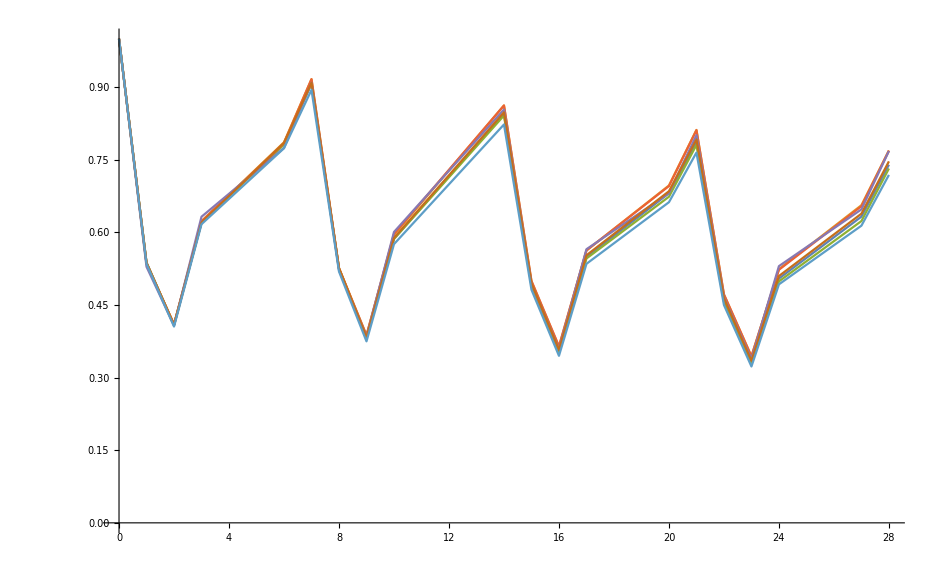

```mathematica
ListLinePlot[tests]
```

```mathematica
FindPeaks[test1[[All,2]]]
```

(1 | 1.
6 | 0.909131
10 | 0.853818
15 | 0.80098
20 | 0.768123)

```mathematica
(*dummy*)
dummy={{0.0,1.0},{1.0,0.537575360285},{2.0,0.405089197756},{3.0,0.607358570778},{6.0,0.786844833814},{7.0,0.900818013731},{8.0,0.527595561916},{9.0,0.38386430792},{10.0,0.580015048383},{14.0,0.841501706811},{15.0,0.499175698926},{16.0,0.358865528586},{17.0,0.547125293007},{20.0,0.698513515142},{21.0,0.797367378184},{22.0,0.464449359249},{23.0,0.334571152531},{24.0,0.504980739829},{27.0,0.648402986281},{28.0,0.747991811452}};
dummyWeekends={{0,1.0},{1,0.988108605607},{2,0.983211739133},{3,0.979649502611},{4,0.97750794092},{5,0.975333270618},{6,0.969732597249},{7,0.966422300635},{8,0.962731475915},{9,0.958524832902},{10,0.95517722925},{11,0.952750618946},{12,0.948323834979},{13,0.943257165822},{14,0.939581872042},{15,0.936353055213},{16,0.932594917616},{17,0.92880386461},{18,0.926756299569},{19,0.921722558833}};
actual={{0.0,1.0},{1.0,0.534661014322},{2.0,0.40552240845},{3.0,0.61697128859},{6.0,0.773850087462},{7.0,0.894453361084},{8.0,0.519211961034},{9.0,0.374978749448},{10.0,0.575786279148},{14.0,0.822944281974},{15.0,0.481617236182},{16.0,0.345095870371},{17.0,0.535094565924},{20.0,0.662390728893},{21.0,0.764902112368},{22.0,0.450065583685},{23.0,0.32304644876},{24.0,0.492699996426},{27.0,0.613915111774},{28.0,0.718801373971}};
```

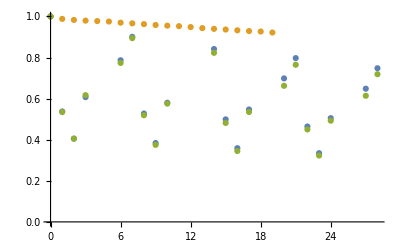

```mathematica
ListPlot[{dummy,dummyWeekends,actual}]
```

```mathematica
ω=(2π)/(24*3600)
R=6.37*10^6
lat=30*π/180
```

π/43200

6.37×10^6

π/6

```mathematica
t[h_]:=1/ω ArcCos[(R Cos[lat])/(R Cos[lat]+h)]
```

```mathematica
t[20]
```

37.0278

```mathematica
t[1500]
```

320.635

```mathematica
ArcCos[(R Cos[lat])/(R Cos[lat]+12000)]*180/π
```

3.77572

```mathematica
Subscript[θ, crit]=360/(2π)ArcCos[R/(R+12000)](*b/c radians*)
```

3.51413

```mathematica
ArcCos[
```